```mathematica
f[m_,h_]:=(m^2-1)^2-m*h
```

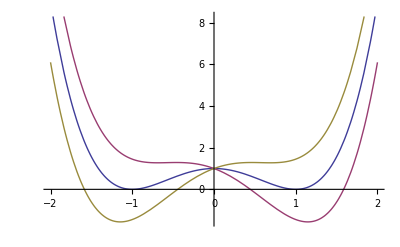

```mathematica
Plot[{f[x,0],f[x,1.45],f[x,-1.45]},{x,-2,2}]
```

```mathematica
sol=Solve[D[f[m,h],m]==0,m]
```

{{m→2/(3^(1/3) (9 h+√3 √(-64+27 h^2))^(1/3))+((9 h+√3 √(-64+27 h^2))^(1/3))/(2 3^(2/3))},{m→-(1+ⅈ √3)/(3^(1/3) (9 h+√3 √(-64+27 h^2))^(1/3))-((1-ⅈ √3) (9 h+√3 √(-64+27 h^2))^(1/3))/(4 3^(2/3))},{m→-(1-ⅈ √3)/(3^(1/3) (9 h+√3 √(-64+27 h^2))^(1/3))-((1+ⅈ √3) (9 h+√3 √(-64+27 h^2))^(1/3))/(4 3^(2/3))}}

```mathematica
InputForm[m/.sol[[1]]]
```

2/(3^(1/3)*(9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3)) + 
 (9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3)/(2*3^(2/3))

```mathematica
InputForm[m/. sol[[3]]]
```

-((1 - I*Sqrt[3])/(3^(1/3)*(9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3))) - 
 ((1 + I*Sqrt[3])*(9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3))/(4*3^(2/3))

```mathematica
InputForm[m/. sol[[2]]]
```

-((1 + I*Sqrt[3])/(3^(1/3)*(9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3))) - 
 ((1 - I*Sqrt[3])*(9*h + Sqrt[3]*Sqrt[-64 + 27*h^2])^(1/3))/(4*3^(2/3))

```mathematica
m1[h_]:=2/(3^(1/3)*(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3))+(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3)/(2*3^(2/3))
m2[h_]:=-((1-I*Sqrt[3])/(3^(1/3)*(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3)))-((1+I*Sqrt[3])*(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3))/(4*3^(2/3))
m3[h_]:=-((1+I*Sqrt[3])/(3^(1/3)*(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3)))-((1-I*Sqrt[3])*(9*h+Sqrt[3]*Sqrt[-64+27*h^2])^(1/3))/(4*3^(2/3))
```

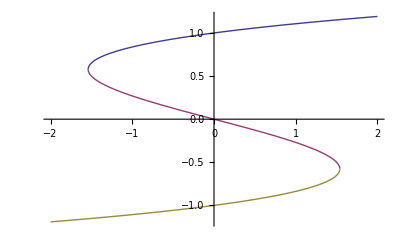

```mathematica
Plot[{m1[h],m2[h],m3[h]},{h,-2,2}]
```

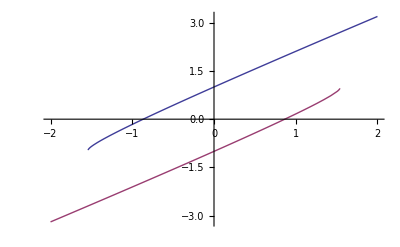

```mathematica
Plot[{h+m1[h],h+m3[h]},{h,-2,2}]
```